## Going through, taking out all $SSS... globals, putting them into an <||>

#### This fails, because for some reason doing the substitution Last[ans["TEvolution"]] /. ans["TRuleSet"] does not correctly perform the needed side jobs, such as incrementing ans["TagIndex"].

#### No time to debug, so I'm reverting to using a few of the $SSS... globals, but in both SSSInitialize and SSSSingleStep I'll load and unload them from the association values. => TestSSSAssoc.1.nb

```mathematica
Clear[FromAlpha,ToAlpha,SSSConvert,SSSStrip];
FromAlpha[string_String] :=(ToCharacterCode[string]-65);  
ToAlpha[l:{___Integer}] := FromCharacterCode[l+65];

Attributes[s]=Flat;
SSSConvert[string_String] := s @@ FromAlpha[string];
SSSConvert[s[x___]] := ToAlpha[{x}];
SSSConvert::usage="Converts SSS (sequential substitution system) states between s- and string-formats, using the functions FromAlpha and ToAlpha.";

SSSStrip[x_s] := SSSConvert[x⟦All,1⟧] /; MatrixQ[List@@x]    (* if dim=2, take only 1st component, and convert *)
SSSStrip[x_s] := ""  /; Length[List@@x]==0     (* treat empty string case *) 

SSSStrip::usage="SSSStrip[StyleBox[\"state\",FontSlant->\"Italic\"]] strips out tags from a StyleBox[\"state\",FontSlant->\"Italic\"] given in tagged SSS (sequential substitution system) format and returns it in string format.";
```

```mathematica
ToCharacterWeights[s_String] := (1+FromAlpha[s]);
FromCharacterWeights[l:{___Integer}] := ToAlpha[l-1];
(* Note: To avoid breaking the ruleset (un-)rank functions, avoid the temptation to define:  
ToCharacterWeights[""] = 0;  FromCharacterWeights[{0}]="";  *)
StringWeight[s_String] := Plus @@ ToCharacterWeights[s];
RuleSetWeight[rs_List] := Plus @@ (StringWeight /@ Flatten[rs /. Rule->List]);
RuleSetLength[rs_List] := Plus @@ (StringLength /@ Flatten[rs /. Rule->List]);
```

$MaxColor = 6;

(1) Just remove $MaxColor.  
(2) Add maxColor parameter to myColors, patternPrint, SSSRuleIcon).

Come back and work this through more carefully later.

```mathematica
Clear[myColors,myColorOptions,patternPrint,SSSRuleIcon]
```

```mathematica
myColorOptions[maxColor_Integer]:=Sequence[ColorRules->{0->LightGray},ColorFunction->(Hue[(#-1)/maxColor]&),ColorFunctionScaling->False];
```

```mathematica
patternPrint[pattern_,mxClr_Integer,opts___] := ArrayPlot[{{##}}& @@pattern,myColorOptions[mxClr],Mesh->True,opts,ImageSize->{Automatic,20}];
```

```mathematica
Clear[SSSRuleIcon];
SSSRuleIcon[(rule_String|rule_Rule|rule_RuleDelayed),x___]:=SSSRuleIcon[{rule},x];

SSSRuleIcon[rules_List,x___]:=SSSRuleIcon[Map[SSSConvert,rules,{-1}],x] /; !FreeQ[rules,_String,Infinity];

SSSRuleIcon[rules_List,mxClr_Integer:6,opts___] := Panel[Grid[Map[patternPrint[#,mxClr,opts]&,rules,{2}] /. 
{Rule[x_,y_]:>{x,"→",y},RuleDelayed[x_,y_]:>{x,":>",y}}, (* invisible AlignmentMarkers! *)
Alignment->Left],"Substitution Rule"<>If[Length[rules]>1,"s:",":"]] /; FreeQ[rules,_String,Infinity];
```

```mathematica
SSSRuleIcon::usage="SSSRuleIcon[rule(s),maxColor] generates an icon for a sequential substitution system (SSS) rule or set of rules.";
```


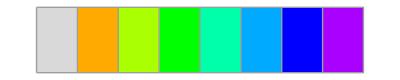
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

```mathematica
SSSRuleIcon[{"A"->"B",""->"ACDEFGHI"},9]
```

```mathematica
Clear[SSSNewRule];
SSSNewRule[rulenum_Integer,(rule_Rule | rule_RuleDelayed)] := Module[{lhs,rhs,lhsNames,newlhs,newrhs1,newrhs2},
{lhs,rhs}=List@@rule;
lhsNames = Table[Unique[lhsTag],{StringLength[lhs]}];
newlhs=ToString[s@@Transpose[{FromAlpha[lhs],ToString@#<>"_"& /@ lhsNames}]];
newrhs1=("AppendTo[ans[\"ConnectionList\"], "<>ToString[lhsNames]<>" → ans[\"TagIndex\"] + "<>ToString[Range@StringLength@rhs-1]<>"]; ");
newrhs2=ToString[SSSConvert[rhs] /. n_Integer :> {n,"ans[\"TagIndex\"]++"}];
ToExpression[newlhs<>" :> ("<>"AppendTo[ans[\"RulesUsed\"],"<>ToString@rulenum<>"];"<>newrhs1<>newrhs2<>")"]];
SSSNewRule[rules_List] := Append[MapIndexed[SSSNewRule[First[#2],#1]&,rules],___:>
AppendTo[ans["RulesUsed"],0]];
SSSNewRule::usage= 
"SSSNewRule[rule(s)] generates the needed rules for the tagged SSS (sequential substitution system) from the ruleset of rules given in string-format: e.g., \"BA\"→\"ABA\"";
```

```mathematica
SSSNewRule[{"ABA"->"AAB","A"->"ABA"}]
```

```mathematica
Clear[SSSInitialize];
Options[SSSInitialize]={Mode->Silent};
SyntaxInformation[SSSEvolve]={"ArgumentsPattern"->{OptionsPattern[]}};

SSSInitialize[rs:{___Rule},state_String,opts:OptionsPattern[] (* Mode -> Silent | Quiet | Loud *)] :=
Module[{ans=<|"Net"->{},"OutDegreePotential"->{},"OutDegreeRemaining"->{},"OutDegreeActual"-> {},
"InDegree"-> {},"ConnectionList"->{},"Verdict"->"OK", "RulesUsed"->{},"CellsDeleted"->{},
"Distance"->{0}|>}, (* initial setup *)
AssociateTo[ans,{
"MaxColor"->Max[Flatten[{6,ToCharacterWeights /@ Flatten[rs/.Rule->List]}]],
"TagIndex"->StringLength[state]+1,
"TEvolution"->{s@@Transpose[{#,Range[Length[#]]}& @ FromAlpha[state]]},
"Evolution"->{state}, "RuleSet"->rs, "TRuleSet"->SSSNewRule[rs],
"RuleSetWeight"->RuleSetWeight[rs], "RuleSetLength"->RuleSetLength[rs]
}];
AppendTo[ans["TEvolution"],Last[ans["TEvolution"]]/.ans["TRuleSet"]];
Switch[ Last[ans["RulesUsed"]], (* can also test if Length[ans["ConnectionList"]]==0 *)
0,ans["TEvolution"]=Most[ans["TEvolution"]]; (* toss last duplicate entry *)
      ans["Verdict"]="Dead";
      If[ OptionValue[Mode]==Loud,Print["Error: No evolution possible starting from \""<>state<>"\" using ruleset: ",rs]];
      Return[ans (* but already including "Verdict" = Dead *)],
_, AppendTo[ans["Evolution"],SSSStrip[Last[ans["TEvolution"]]]]; (* add last entry *)
       If[ OptionValue[Mode]==Loud,Print["Successful initialization of ruleset: ",rs,", evolution: ",ans["Evolution"]]]
];
(* updateDegrees for the first step: *)
AppendTo[ans["InDegree"],Length[ans["ConnectionList"]⟦-1,1⟧]];  (* # cells killed by this event = in-degree *)
(* calculate potential outdegree of new event, append to list *)
AppendTo[ans["OutDegreePotential"],Length[ans["ConnectionList"]⟦-1,-1⟧]]; (* # of cells created by last rule *)
AppendTo[ans["OutDegreeRemaining"],Last[ans["OutDegreePotential"]]];
AppendTo[ans["OutDegreeActual"],0];
AppendTo[ans["CellsDeleted"],Flatten[Position[ans["TEvolution"]⟦-2⟧,{_,#}]& /@ans["ConnectionList"]⟦-1,1⟧]];  (* Note positions of entries with tags indicated, add to the list *)
ans  (* Return the association created *)
];
```

```mathematica
sss=SSSInitialize[{"ABA"->"AAB","A"->"ABA"}, "A",Mode->Loud];
```

Successful initialization of ruleset: {ABA→AAB,A→ABA}, evolution: {A,ABA}

```mathematica
sss["TRuleSet"]
```

{s[{0,lhsTag$23133_},{1,lhsTag$23134_},{0,lhsTag$23135_}]:>(AppendTo[ans[RulesUsed],1];AppendTo[ans[ConnectionList],{lhsTag$23133,lhsTag$23134,lhsTag$23135}→ans[TagIndex]+{0,1,2}];s[{0,ans[TagIndex]++},{0,ans[TagIndex]++},{1,ans[TagIndex]++}]),s[{0,lhsTag$23137_}]:>(AppendTo[ans[RulesUsed],2];AppendTo[ans[ConnectionList],{lhsTag$23137}→ans[TagIndex]+{0,1,2}];s[{0,ans[TagIndex]++},{1,ans[TagIndex]++},{0,ans[TagIndex]++}]),___:>AppendTo[ans[RulesUsed],0]}

```mathematica
sss["TagIndex"]
```

2

```mathematica
sss["Evolution"]=Most[sss["Evolution"]]
```

{A}

```mathematica
sss["TEvolution"]=Most[sss["TEvolution"]]
```

{s[{0,1}]}

```mathematica
sss["TRuleSet"]
```

```mathematica
{ s[{0,lhsTag$23133_},{1,lhsTag$23134_},{0,lhsTag$23135_}]:>(AppendTo[ans["RulesUsed"],1];AppendTo[ans["ConnectionList"],{lhsTag$23133,lhsTag$23134,lhsTag$23135}->ans["TagIndex"]+{0,1,2}];s[{0,ans["TagIndex"]++},{0,ans["TagIndex"]++},{1,ans["TagIndex"]++}]),s[{0,lhsTag$23137_}]:>(AppendTo[ans["RulesUsed"],2];AppendTo[ans["ConnectionList"],{lhsTag$23137}->ans["TagIndex"]+{0,1,2}];s[{0,ans["TagIndex"]++},{1,ans["TagIndex"]++},{0,ans["TagIndex"]++}]),___:>AppendTo[ans["RulesUsed"],0]}
```

```mathematica
Module[{ans=sss},
Last[ans["TEvolution"]]/.ans["TRuleSet"]
]
```

s[{0,ans[TagIndex]++},{1,ans[TagIndex]++},{0,ans[TagIndex]++}]

```mathematica
sss["TagIndex"]++
```

4

```mathematica
sss["TagIndex"]++
```

```mathematica
{s[{0,1}],s[{0, ans["TagIndex"]++},{1,ans["TagIndex"]++},{0,ans["TagIndex"]++}]}
```

```mathematica
{}
```

```mathematica
Keys[%51]
```

{Net,OutDegreePotential,OutDegreeRemaining,OutDegreeActual,InDegree,ConnectionList,Verdict,RulesUsed,CellsDeleted,Distance,MaxColor,TagIndex,TEvolution,Evolution,RuleSet,TRuleSet,RuleSetWeight,RuleSetLength}

```mathematica
%51["Evolution"]
```

{A,ABA}

```mathematica
SSSInitialize::usage = "variable = SSSInitialize[ruleset, string, (mode)] attempts to perform the necessary initializion steps to generate sequential substitution system (SSS) evolutions and networks,\nstarting with a ruleset (e.g., {\"BA\"→\"ABA\"}) and an initial state string (e.g., \"BABA\").  The True|False return value indicates whether initialization was successful.\n\nIf omitted, mode defaults to \"Silent\", suppressing the short error or success message.\n\nThe following global variables are reset by this operation:\n\n$SSSNet:\t\t\t\tthe causal network of the current SSS,\n$SSSInDegree:\t\t\tthe list of in-degrees for each node,\n$SSSOutDegreeActual:\t\tthe list of currently found out-degrees for each node,\n$SSSOutDegreePotential:\t\tthe list of maximum possible out-degrees for each node,\n$SSSOutDegreeRemaining:\tthe list of numbers of possible remaining out-connections for each node,\n$SSSConnectionList:\t\tthe current list of all causal network connections,\n$SSSDistance:\t\t\tthe list of minimum distances from the current node back to the starting node.\n$SSSTagIndex:\t\t\tthe current tag index being used,\n$SSSTEvolution:\t\t\tthe complete evolution of the tagged SSS so far,\n$SSSEvolution:\t\t\tthe stripped (tagless) version of $SSSTEvolution,\n$SSSRuleSet:\t\t\tthe ruleset used for creating the SSS,\n$SSSTRuleSet:\t\t\tthe version of $SSSRuleSet (created by the function SSSNewRule) used to build $SSSTEvolution,\n$SSSRuleSetWeight:\t\tthe total weight of $SSSRuleSet,\n$SSSRuleSetLength:\t\tthe total length of $SSSRuleSet,\n$SSSRulesUsed:\t\tthe list of rules used\n$SSSCellsDeleted:\t\tthe list of cells in the state string deleted at each step,\n$SSSVerdict:\t\t\tset to \"Dead\" | \"Repeating\" as soon as the future of the SSS becomes clear.";
```

```mathematica
SSSSingleStep::usage=
"SSSSingleStep performs a single step of the current sequential substitution system (SSS) evolution (if not already dead), applying the current SSS ruleset (saved in $SSSRuleSet and $SSSTRuleSet) to the most recent state, the last entry in $SSSTEvolution and $SSSEvolution.  This operation updates the global variables $SSSConnectionList, $SSSTagIndex, $SSSTEvolution, $SSSEvolution, $SSSRulesUsed, $SSSVerdict, $SSSOutDegreePotential, $SSSOutDegreeRemaining, $SSSOutDegreeActual,$SSSCellsDeleted,$SSSDistance.  Use SSSInitialize to set up the global variables.";
```

```mathematica
Clear[SSSSingleStep];
SSSSingleStep := Module[{cd, ri, pri, rs, prs,len,startingEvents},
If[$SSSVerdict==="Dead",Return[False]];  (* if already dead, do nothing, return *)

(* do the actual evolution step *)
AppendTo[$SSSTEvolution,Last[$SSSTEvolution]/.$SSSTRuleSet];
 If[Last[$SSSRulesUsed]==0,$SSSVerdict="Dead";$SSSTEvolution=Most[$SSSTEvolution]; Return[False]];
AppendTo[$SSSEvolution,SSSStrip[Last[$SSSTEvolution]]];

If[!MatchQ[$SSSVerdict,"Repeating"],  (* to limit wasted time, don't do this if the verdict is already in! *)
If[Length[Flatten@Position[$SSSEvolution,Last[$SSSEvolution]]]>1, $SSSVerdict="Repeating"]]; 

(* Now update globals:  first the part that is done for each step, including the first one (by SSSInitialize): *)
updateDegrees; (* $SSSOutDegreePotential, $SSSOutDegreeRemaining, $SSSOutDegreeActual, [omitted: $SSSMatchLengthHistory, $SSSHistory] *)

(* now the steps that are only done for non-initial steps, comparing to previous entries in $SSSConnectionList: *)
len=Length[$SSSConnectionList];
startingEvents=Flatten[If[Length[#]>0,First[First[#]],#]& /@ (Position[$SSSConnectionList⟦;;-2⟧,#]& /@ $SSSConnectionList⟦-1,1⟧)];
$SSSOutDegreeActual⟦#⟧++& /@ startingEvents; (* update out-degee list for events involved *)
$SSSOutDegreeRemaining⟦#⟧--& /@ startingEvents; (* update out-degee list for events involved *)
$SSSNet=Join[$SSSNet,#->len& /@ startingEvents];           (* add new links to the causal network *)
AppendTo[$SSSDistance,Min[$SSSDistance⟦startingEvents⟧]+1];  (* Find minimum path length of cause nodes, add 1 for path lengths of result nodes *)
Return[True];
];
```

### Public:

```mathematica
Clear[SSSEvolve];
Options[SSSEvolve]={EarlyReturn->False, Mode->Silent};
SyntaxInformation[SSSEvolve]={"ArgumentsPattern"->{OptionsPattern[]}};

SSSEvolve[n_Integer/;n>0,opts:OptionsPattern[]] := (
If[OptionValue[EarlyReturn] ,
Do[If[MatchQ[$SSSVerdict, ("Dead"|"Repeating")],Break[],SSSSingleStep],{n}], (* check before each step *)
Do[SSSSingleStep,{n}]   (* just do it *)
];
If[OptionValue[Mode]==Loud,Print[$SSSVerdict]];
True
)
```

```mathematica
SSSEvolve::usage="SSSEvolve[n] generates an additional n levels of the current SSS (sequential substitution system), which must have been previously initialized using SSSInitialize.  Use the option EarlyReturn → True to allow early termination for repeating cases.  (SSSSinglestep immediately returns anyway if the SSS is dead.)  In Loud mode, prints the current verdict, \"OK\" means none known.  Global variables set up by SSSInitialize are updated, with $SSSEvolution containing the tagless SSS, $SSSConnectionList the updated causal network connection list, etc.  mode can be Silent, Quiet, or Loud.";
```

```mathematica
Options[SSSDisplay]=
{HighlightMethod->True,RulePlacement->Bottom,Mesh->True,NetSize->{Automatic,400},SSSSize->{Automatic,300},IconSize->{Automatic,20},ImageSize->Automatic,NetMethod->GraphPlot,
Max->∞,SSSMax->Automatic,NetMax->Automatic,
Min->1,SSSMin->Automatic,NetMin->Automatic, 
Sequence@@Union[Options[TreePlot],Options[GraphPlot],Options[GraphPlot3D],Options[LayeredGraphPlot]]};
SyntaxInformation[SSSDisplay]={"ArgumentsPattern"->{OptionsPattern[]}};
```

```mathematica
SSSDisplay[opts:OptionsPattern[]] := Module[{HlM,mesh,IcS,ImS,SS,NS,RP,NM,doGP,doLGP,doTP,doGP3D,doSSS,myNet,ans,cellsToHighlight,rulesApplied,mx,netmx,sssmx,mn,netmn,sssmn,hs,start,ev,vrtxs,net,grph,DE},

HlM =If[#===True,Number,#]& @ OptionValue[HighlightMethod]; 
RP=OptionValue[RulePlacement];
mesh=OptionValue[Mesh];
SS = OptionValue[SSSSize];
IcS = OptionValue[IconSize];
ImS = OptionValue[ImageSize];
NS = OptionValue[NetSize];
NM=OptionValue[NetMethod];
DE= OptionValue[DirectedEdges];

mx=OptionValue[Max];
If[mx===Automatic,mx=∞];
sssmx=OptionValue[SSSMax]; 
If[sssmx===Automatic,sssmx=mx];
netmx=OptionValue[NetMax]; 
If[netmx===Automatic,netmx=mx];

mn=OptionValue[Min];
If[mn===Automatic,mn=1];
sssmn=OptionValue[SSSMin]; 
If[sssmn===Automatic,sssmn=mn];
netmn=OptionValue[NetMin]; 
If[netmn===Automatic,netmn=mn];

start=1;

vrtxs =Annotation[#,VertexWeight->$SSSDistance⟦#⟧]&/@Range[Max[start,netmn],Min[netmx,Length[$SSSDistance]]];

net=(Select[$SSSNet,And@@Thread[Max[start,netmn]≤List@@#≤netmx]&] /. n_Integer:>(n+1-start));

(*
If[UD||(DM<∞),net=(net /.nn_Integer:>Subscript[$SSSDistance⟦nn⟧,Style[nn,Tiny]])];
If[DM<∞,
net=Cases[net,r:Rule[Subscript[_?(#≤DM&),_],Subscript[_?(#≤DM&),_]]:> r];
If[!UD,net=(net /. Subscript[_,Style[n_Integer,_]]:>n)]
];
*)

grph=Graph[vrtxs,net,DirectedEdges->DE];

doGP=doLGP=doTP =doGP3D=False;doSSS=True;
If[MemberQ[NM,All,{0,∞}],doGP=doLGP=doTP=doGP3D=True];
If[MemberQ[NM,GraphPlot,{0,∞}],doGP=True];
If[MemberQ[NM,LayeredGraphPlot,{0,∞}],doLGP=True];
If[MemberQ[NM,TreePlot,{0,∞}],doTP=True];
If[MemberQ[NM,GraphPlot3D,{0,∞}],doGP3D=True];
If[MemberQ[NM,NoSSS,{0,∞}],doSSS=False];

If[$SSSVerdict=="Dead",doGP=doLGP=doTP=doGP3D=False];

cellsToHighlight=Flatten[MapIndexed[{#1,#2⟦1⟧}&,Reverse@$SSSCellsDeleted⟦Max[start,sssmn];;Min[sssmx,Length[$SSSEvolution]]-1⟧,{2}],1];
rulesApplied=Reverse@$SSSRulesUsed⟦Max[start,sssmn];;Min[sssmx,Length[$SSSEvolution]]-1⟧;

ans = 
ArrayPlot[(FromAlpha/@ $SSSEvolution⟦Max[start,sssmn];;Min[sssmx,Length[$SSSEvolution]]⟧)/. 0->LightGray,myColors,Mesh->mesh,ImageSize->SS,
Epilog->Switch[HlM,
Dot,Disk[#+0.5{-1,1},.18]& /@ cellsToHighlight,
Frame,{EdgeForm[Thick],FaceForm[],Rectangle[#-{1,0}]& /@ cellsToHighlight},
Number,Text @@@ (cellsToHighlight /. {x_Integer,y_Integer}:>{rulesApplied⟦y⟧,{x,y}+.5{-1,1}}),
_,{}]
];
Row[Flatten@{
If[!doSSS,{},Pane[
Switch[RP,
Right, Grid[{{ans,SSSRuleIcon[$SSSRuleSet,ImageSize->IcS]}}],
Left, Grid[{{SSSRuleIcon[$SSSRuleSet,ImageSize->IcS],ans}}], 
Bottom|True, Grid[{{ans},{SSSRuleIcon[$SSSRuleSet,ImageSize->IcS]}}], 
Top,  Grid[{{SSSRuleIcon[$SSSRuleSet,ImageSize->IcS]},{ans}}], 
_,ans],ImageSize->ImS,ImageSizeAction->"ShrinkToFit"]],
If[doGP,GraphPlot[grph,GraphLayout->"SpringElectricalEmbedding",
Sequence@@Flatten[{ImageSize->NS,FilterRules[{opts}, Options[GraphPlot]],
VertexSize->Large,VertexLabels->Placed[Automatic,Center]}]],{}],
If[doLGP,LayeredGraphPlot[grph,Sequence@@Flatten[{ImageSize->NS,FilterRules[{opts}, Options[LayeredGraphPlot]],VertexSize->Large,VertexLabels->Placed[Automatic,Center]}]],{}],
If[doTP,TreePlot[grph,Top,1,Sequence@@Flatten[{ImageSize->NS,FilterRules[{opts}, Options[TreePlot]],VertexSize->Large,VertexLabels->Placed[Automatic,Center],DirectedEdges->True}]],{}],
If[doGP3D,GraphPlot3D[grph,GraphLayout->"SpringElectricalEmbedding",Sequence@@Flatten[{ImageSize->NS,FilterRules[{opts}, Options[GraphPlot3D]],VertexSize->Large,VertexLabels->Placed[Automatic,Center]}]],{}]
},"  "]]
```

```mathematica
SSS[rs:{___Rule},init_String,n_Integer?Positive,opts___] := 
If[SSSInitialize[rs,init,Mode->Silent], 
SSSEvolve[n-1,Sequence@@FilterRules[{opts},Options[SSSEvolve]]]; 
SSSDisplay[Sequence@@FilterRules[{opts},Options[SSSDisplay]]]
];
Options[SSS]=Join[Options[SSSEvolve],Options[SSSDisplay]];
SyntaxInformation[SSS]={"ArgumentsPattern"->{_,_,_,OptionsPattern[]}};
```

```mathematica
SSS::usage="SSS[rule, init, n, opts] creates and displays a sequential substitution system (SSS) and its causal network, using ruleset starting with the state init (using string notation), allowing the SSS to evolve for n steps.  Use the option EarlyReturn to give/deny permission to quit early if the SSS can be identified as dead or (pseudo-)repeating.)  Any other options given are passed on to SSSDisplay.

(After creation the current SSS can be displayed or manipulated without rebuilding, using SSSDisplay, SSSAnimate, or directly using the global variables $SSSRuleSet, $SSSEvolution and $SSSNet.)";
```

```mathematica
Clear[SSSInteractiveDisplay,dynamicLabel];
dynamicLabel[lbl_,max_]:=Dynamic[If[Clock[{1,max,1},max]==lbl,Framed[lbl,Background->Green,RoundingRadius->Scaled[.5]],lbl]];
SSSInteractiveDisplay := With[{mxmx=Max[List @@@ $SSSNet]},
Manipulate[
If[Head[vl]===List,vp=Automatic];
If[mx<mn,mx=mn+1];
If[sssmx<sssmn,sssmx=sssmn+1];
If[ntmx<ntmn,ntmx=ntmn+1];
args={Min->mn,Max->mx,SSSMin->(sssmn/. 0->Automatic),SSSMax->(sssmx/. mxmx+1->Automatic),NetMin->(ntmn/. 0->Automatic),NetMax->(ntmx/.mxmx+1->Automatic),HighlightMethod->hlm,RulePlacement->sr,NetMethod->Flatten[{nm,If[no,{NoSSS},{}]}],ImageSize->is,NetSize->{Automatic,ns},SSSSize->{Automatic,ssss},IconSize->{Automatic,cns},VertexSize->vs,
VertexLabels->If[vp===Automatic,vl,Placed[vl,vp]],
DirectedEdges->dir};
SSSDisplay@@args,
Grid[{{
Control[{{hlm,Number,"HighlightMethod"},{Dot,Frame,Number,None}}],
Control[{{sr,Bottom,"RulePlacement"},{Bottom,Top,Left,Right,None}}],
Control[{{nm,GraphPlot,"NetMethod"},{GraphPlot,LayeredGraphPlot,TreePlot,GraphPlot3D,All}}],
Button["Save these options",
CellPrint[ExpressionCell[Defer[SSSDisplay][Sequence@@args],"Input"]];
SelectionMove[InputNotebook[],Previous,Cell];
]
}},Spacings->2],
{args,{},ControlType->None},
Grid[{{Control[{{mn,1,"Min"},1,mxmx,1,Appearance->"Labeled"}],Control[{{mx,mxmx,"Max"},1,mxmx,1,Appearance->"Labeled"}],
Row[{
Control[{{dir,False,"directed"},{False,True}}],"    ",
Control[{{no,False,"NoSSS"},{False,True}}]
}]
},
{Control[{{sssmn,0,"SSSMin"},0,mxmx,1,Appearance->"Labeled"}],Control[{{sssmx,mxmx+1,"SSSMax"},0,mxmx+1,1,Appearance->"Labeled"}],"(a NetMethod option)"},{Control[{{ntmn,0,"NetMin"},0,mxmx,1,Appearance->"Labeled"}],Control[{{ntmx,mxmx+1,"NetMax"},0,mxmx+1,1,Appearance->"Labeled"}],
Control[{{vs,Automatic,"VertexSize →"},{Automatic,Tiny,Small,Medium,Large,0.8->"Huge"},ControlType->PopupMenu}]
},
{Control[{{ssss,220,"SSSSize"},10,500,Appearance->"Labeled"}],
Control[{{is,350,"ImageSize"},10,500,Appearance->"Labeled"}],Control[{{vl,Automatic,"VertexLabels →"},{Automatic,None,"Name","VertexWeight",
((#->Placed[#,Center,Function[{arg},dynamicLabel[arg,ntmx]]])&/@Range[ntmn+1,ntmx-1])->"Dynamic"},ControlType->PopupMenu}]},
{Control[{{cns,20,"IconSize"},10,50,Appearance->"Labeled"}],Control[{{ns,300,"NetSize"},10,800,Appearance->"Labeled"}],
Control[{{vp,Automatic,"Placed"},
{Automatic,Center,Before,After,Below,Above,Tooltip,StatusArea}}]}
},Alignment->Right,Spacings->2]
]]
SSSInteractiveDisplay::usage="SSSInteractiveDisplay provides an interactive display of the current SSS and causal network, with controls for easy adjustment of common options.  Click the button to create a SSSDisplay object with the selected options.";
```

If everything above loaded correctly, the following lines will work:

```mathematica
SSS[{"ABA"->"AAB","A"->"ABA"}, "A",44,SSSMax->15,NetMethod->GraphPlot]
```

```mathematica
SSSDisplay[SSSMax->15,SSSSize->{120,Automatic},NetMax->27,NetSize->{Automatic,350},VertexLabels->Placed["Name",Tooltip],VertexSize->Medium]
```